## Datos de Google Earth VS Curvas de Nivel

```mathematica
data=Import["C:\\Users\\FatalRaincloud\\Documents\\School\\Sum 42\\Métodos Numéricos en Ingeniería\\NevadoToluca.csv"];
```

```mathematica
data//Dimensions
```

{28,10}

```mathematica
Grid[data];
```

```mathematica
data01=data[[2;;28, {3,4,5}]];
```

```mathematica
Grid[data01, Frame-> All, ItemSize->Automatic, Background->{None, {{LightPurple, LightBlue}}}];
```

```mathematica
ListPlot3D[data01, Mesh->False, InterpolationOrder->3, ColorFunction->"GreenBrownTerrain"]
```

-Graphics3D-

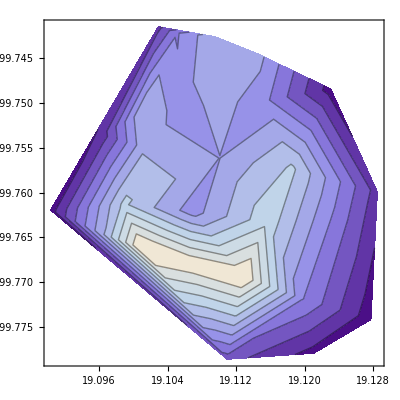

```mathematica
ListContourPlot[data01, InterpolationOrder->3,Contours->10]
```